```mathematica
Manipulate[
lv=NDSolve[
{Res'[t]==Res[t]*(1-Res/K)-Xc*Yc*((Res[t]*Con[t])/(R0+Res[t]))-ω*Xp*Ypr*((Pred[t]*Res[t])/(R02+(1-ω)* Con[t]+ω*Res[t])),Con'[t]==Xc*Yc*((Res[t]*Con[t])/(R0+Res[t]))-Xc*Con[t]-(1-ω)*Xp*Ypc*((Pred[t]*Con[t])/(C0+(1-ω)* Con[t]+ω*Res[t])),
Pred'[t]==ω*Xp*Ypr*((Pred[t]*Res[t])/(R02+(1-ω)* Con[t]+ω*Res[t]))+ (1-ω)*Xp*Ypc*((Pred[t]*Con[t])/(C0+(1-ω)* Con[t]+ω*Res[t]))-Xp*Pred[t]}
{x[t],y[t], z[t]},{t,0,20}];
Plot[
Evaluate[
{x[t],y[t]}/.lv],
{t,0,20},
PlotRange->All,AxesOrigin->{0,0}],
{{lv,{}},None},
{{x0,10},5,30,1},
{{y0,6},2,20,1},
{{a,1.5},1.,4.},
{{b,1.},1.,4.},
{{c,3.},1.,4.},
{{d,1.},.1,2.}]
```

```mathematica
eqs={
Res'[t]==Res[t]*(1-Res[t]/K)-Xc*Yc*((Res[t]*Con[t])/(R0+Res[t]))-ω*Xpr*Ypr*((Pred[t]*Res[t])/(R02+(1-ω)* Con[t]+ω*Res[t])),
Con'[t]==Xc*Yc*((Res[t]*Con[t])/(R0+Res[t]))-Mc*Con[t]-(1-ω)*Xpc*Ypc*((Pred[t]*Con[t])/(C0+(1-ω)* Con[t]+ω*Res[t])),
Pred'[t]==ω*Xpr*Ypr*((Pred[t]*Res[t])/(R02+(1-ω)* Con[t]+ω*Res[t]))+ (1-ω)*Xpc*Ypc*((Pred[t]*Con[t])/(C0+(1-ω)* Con[t]+ω*Res[t]))-Mp*Pred[t],
Res[0]==1, Con[0]==1, Pred[0]==1};
K=2;
ω=0.5;
Xc=0.05;
Yc=2.9;
Xpr=0.05;
Xpc=0.2;
Ypr=5;
Ypc=2;
R0=0.4;
R02=0.5;
C0=1.5;
Tf = 100000;
Mc = 0.025;
Mp = 0.025;
```

```mathematica
s = NDSolve[eqs, {Res,Con,Pred},{t,0,Tf}]
```

{{Res→InterpolatingFunction[{{0., 100000.}}, <>],Con→InterpolatingFunction[{{0., 100000.}}, <>],Pred→InterpolatingFunction[{{0., 100000.}}, <>]}}

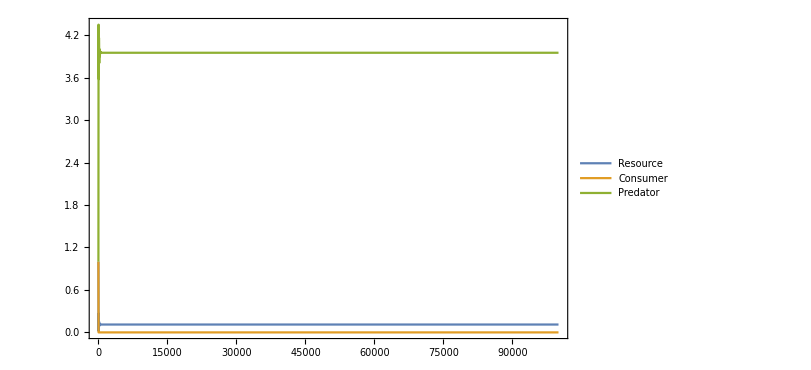

```mathematica
Plot[
Evaluate[{Res[t],Con[t], Pred[t]}/.s],
{t,0,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
```

```mathematica
K=2;
Xc=1;
Mc = 0.025;
tr = 0.03;
tc = 0.5;
tpr = 0.05;
Xp = 0.2;
Mp = 0.025;
α = 0;
Tf = 6000;
eqs={
Res'[t]==Res[t]*(1-Res[t]/K)-Xc*(Res[t]/(1+tr*Res[t]))*Con[t]-Xp*(Res[t]/(1+α*tc*Con[t]+tpr*Res[t]))*Pred[t],
Con'[t]==Xc*(Res[t]/(1+tr*Res[t]))*Con[t]-Mc*Con[t]-Xp*((α*Con[t])/(1+α*tc*Con[t]+tpr*Res[t]))*Pred[t],
Pred'[t]== Xp*Pred[t]*(Res[t]/(1+α*tc*Con[t]+tpr*Res[t])+(α*Con[t])/(1+α*tc*Con[t]+tpr*Res[t]))-Mp*Pred[t],
Res[0]==1, Con[0]==1, Pred[0]==1};
s = NDSolve[eqs, {Res,Con, Pred},{t,0,Tf}]
```

{{Res→InterpolatingFunction[{{0., 6000.}}, <>],Con→InterpolatingFunction[{{0., 6000.}}, <>],Pred→InterpolatingFunction[{{0., 6000.}}, <>]}}

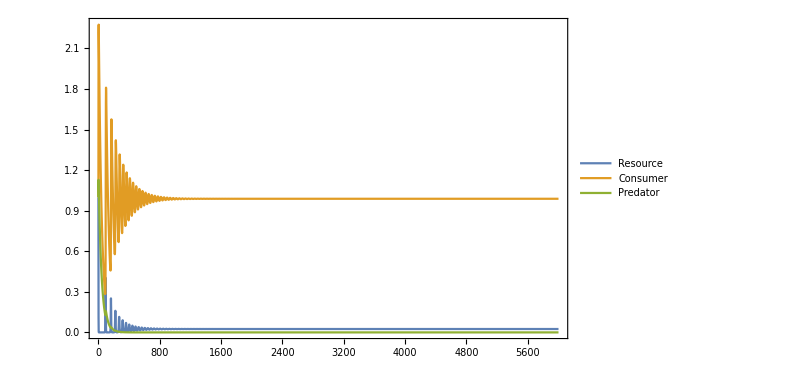

```mathematica
Plot[
Evaluate[{Res[t], Con[t],Pred[t]}/.s],
{t,0,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
```

```mathematica
r=1;
K=2;
A=2;
H=0;
B=1;
h1=1;
h2=2;
e1=0.09;
e2=0.5;
S1=1;
S2=2;
α=1;
M=0.1;
d=0.1;
v=5;
μ=0.001;

Tf = 6000;
eqs={
Res'[t]==r*Res[t]*(1-Res[t]/K)-((A*Res[t])/(1+H*A*Res[t]))*Con[t]-((q[t]*S1*Res[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t]))*Pred[t],
Con'[t]==((B*A*Res[t])/(1+H*A*Res[t]))*Con[t]-M*Con[t]-((S2*α*Con[t])/(1+S1*q[t]*h1*Con[t]+S2*h2*α*Res[t]))*Pred[t],
Pred'[t]==((e1*q[t]*S1*Res[t])/(1+S1*q[t]*h1*Res[t]+S2*h2*α*Con[t])+(e2*S2*α*Con[t])/(1+S1*q[t]*h1*Con[t]+S2*h2*α*Res[t]))*Pred[t]-d*Pred[t],
q'[t]==v*((Res[t]*S1*(e1+Con[t]*S2*(e1*h2-e2*h1)))/(1+S1*h1*Res[t]*q[t]+S2*h2*Con[t])^2)+μ/q[t]-μ/(1-q[t]),
Res[0]==1, Con[0]==1, Pred[0]==1,q[0]==0.5};
s = NDSolve[eqs, {Res,Con, Pred, q},{t,0,Tf}]
```

{{Res→InterpolatingFunction[{{0., 6000.}}, <>],Con→InterpolatingFunction[{{0., 6000.}}, <>],Pred→InterpolatingFunction[{{0., 6000.}}, <>],q→InterpolatingFunction[{{0., 6000.}}, <>]}}

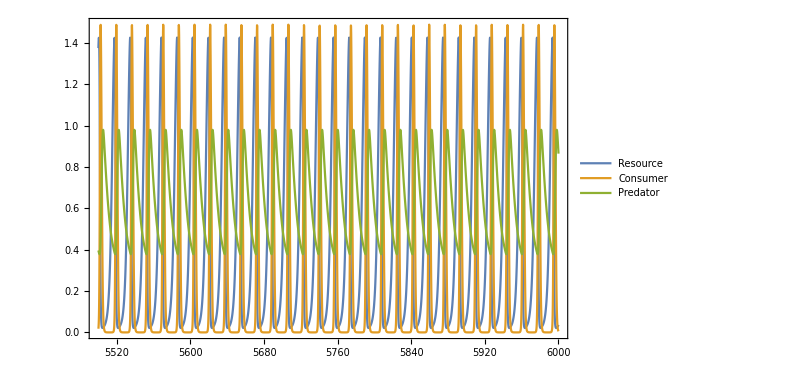

```mathematica
Plot[
Evaluate[{Res[t], Con[t],Pred[t]}/.s],
{t,5500,Tf},
PlotStyle->Automatic,
PlotLegends->{"Resource", "Consumer", "Predator"},
ImageSize->600,
PlotRange->All,
Frame->True]
```